# HW zero Name: Dhruvit Manojkumar Mavani

## 3) Import matrix

```mathematica
A = Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/gemat/gemat12.mtx.gz"]
```

SparseArray[…]

1)  Plotting of matrix A and computing % of non-zeroes

```mathematica
MatrixPlot[A,PlotLegends->Automatic]
```

-Graphics-

```mathematica
33044./4929^2
```

0.00136011

2) Defining b

```mathematica
b = Normal[SparseArray[1->1,4929]];
```

3) Compute third largest magnitude Eigenvalue of A

```mathematica
Eigenvalues[A,{3}]
```

{5.2894-1.20544 ⅈ}

4) Solve Ax = b

```mathematica
x = Inverse[A].Transpose[b];
x[[3]]
```

1.11486

5) Compute 50 largest singular values

```mathematica
y = SingularValueList[A,50];
```

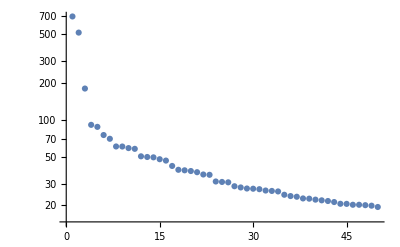

```mathematica
ListLogPlot[y]         (* Log plot of 50 singular values *)
```

6) Time to compute the singular value

```mathematica
AbsoluteTiming[Norm[y]]
```

{0.0000698,923.257}

## 4) A=B transpose(B)

```mathematica
m = 20;
B = RandomReal[{-1,1},{m,m}];
A = B.Transpose[B];
```

1) Compute SVD

```mathematica
{U,S,V} = SingularValueDecomposition[A];
Norm[A-U.S.Transpose[V]]
```

2.34864×10^-14

```mathematica
MatrixPlot[S,PlotLegends->Automatic]
```

-Graphics-

2) Compute QR Decomposition and Plot R

```mathematica
{Q,R} = QRDecomposition[A];
Q = Transpose[Q];
Norm[A-Q.R]       (* Verification of residual being small *)
```

6.70691×10^-15

```mathematica
MatrixPlot[R,PlotLegends->Automatic]
```

-Graphics-

3) Compute a Cholesky Decomposition and Plot L

```mathematica
L = CholeskyDecomposition[A];
```

```mathematica
Norm[A-L.Transpose[L]]/Norm[A]        (* Verification of residual being small *)
```

0.576767

```mathematica
MatrixPlot[L,PlotLegends->Automatic]
```

-Graphics-

4) Compute Eigen decomposition and plot X.transpose(X)

```mathematica
{L,X} = Eigensystem[A];
X = Transpose[X];
Norm[A - V.DiagonalMatrix[L].Inverse[V]]/Norm[A]
```

1.03041×10^-15

```mathematica
Norm[A - X.L.Inverse[X]]
```

Inverse::matsq: Argument {26.539,18.3201,14.7932,12.5946,11.5947,10.3176,8.54006,6.32305,5.67609,4.64789,«10»} at position 1 is not a non-empty square matrix.

```mathematica
MatrixPlot[X.Inverse[X],PlotLegends->Automatic]
```

-Graphics-